```mathematica
Exit[]
```

```mathematica
TrigToExp[Cos[t]^2 Exp[I t]-I Sin[t]]
```

(3 ⅇ^(-ⅈ t))/4+1/4 ⅇ^(3 ⅈ t)

```mathematica
TrigReduce[Cos[t]^2 Exp[I t]-I Sin[t]]
```

1/4 ⅇ^(-ⅈ t) (3+ⅇ^(4 ⅈ t))

```mathematica
c00[t_] = Exp[I t]/Sqrt[2]
c01[t_] = 1/Sqrt[2](Cos[t] Exp[2 I t]-I Sin[t])//FullSimplify
c10[t_] = -I/Sqrt[2]Sin[2t] Exp[I t]//FullSimplify
```

ⅇ^(ⅈ t)/(√2)

(ⅇ^(ⅈ t) Cos[2 t])/(√2)

√2 Cos[t] Sin[t] (-ⅈ Cos[t]+Sin[t])

```mathematica
Assuming[t>0,c00[t] Conjugate[c00[t]] + c01[t] Conjugate[c01[t]]+c10[t] Conjugate[c10[t]]//FullSimplify]
```

1

```mathematica
1/2 Assuming[t>0,c00[t] Conjugate[c00[t]] + c01[t] Conjugate[c01[t]]-c10[t] Conjugate[c10[t]]//FullSimplify]
```

1/2 Cos[2 t]^2

```mathematica
1/2 Assuming[t>0,c00[t] Conjugate[c00[t]] - c01[t] Conjugate[c01[t]]+c10[t] Conjugate[c10[t]]//FullSimplify]
```

1/2 Sin[2 t]^2

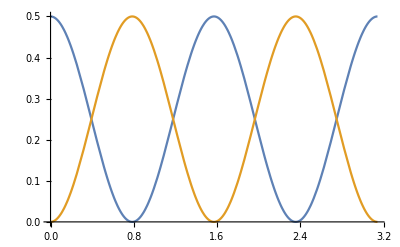

```mathematica
Plot[{1/2 Cos[2 t]^2, 1/2 Sin[2 t]^2},{t,0, π}]
```